## Complete graphs

```mathematica
Table[CompleteGraph[k,VertexLabels->"Name", ImageSize->100, EdgeStyle->Darker[Green],VertexStyle->Red,VertexSize->.2],{k,1,6}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ChromaticPolynomial[CompleteGraph[k],x],{k,1,6}]
```

{x,-x+x^2,2 x-3 x^2+x^3,-6 x+11 x^2-6 x^3+x^4,24 x-50 x^2+35 x^3-10 x^4+x^5,-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6}

## Empty graphs

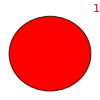
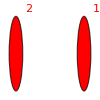
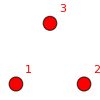
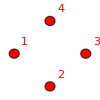
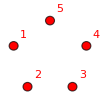
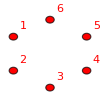

```mathematica
Table[Graph[Range[k],{},VertexLabels->"Name", ImageSize->{100,100}, EdgeStyle->Darker[Green],VertexStyle->Red,GraphLayout->"CircularEmbedding",VertexSize->.2],{k,1,6}]
```

## Stirling transform

```mathematica
allGraphs4[271,"graph"]
```

-Graphics-

```mathematica
repBase4NullBare=Table[allGraphs4[k,"colofourrealnull"]->allGraphs4[k,"graph"],{k,allGraphs4NullAtomKeys}]
```

{n1x2x3x4→-Graphics-,n12x3x4→-Graphics-,n123x4→-Graphics-,n1234→-Graphics-,n124x3→-Graphics-,n12x34→-Graphics-,n13x2x4→-Graphics-,n134x2→-Graphics-,n13x24→-Graphics-,n14x2x3→-Graphics-,n14x23→-Graphics-,n1x23x4→-Graphics-,n1x234→-Graphics-,n1x24x3→-Graphics-,n1x2x34→-Graphics-}

```mathematica
repBase5Bare=Table[allGraphs5[k,"colofour"]->allGraphs5[k,"graph"],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5→-Graphics-,v1x2x3x45→-Graphics-,v1x2x35x4→-Graphics-,v1x2x34x5→-Graphics-,v1x2x345→-Graphics-,v1x25x3x4→-Graphics-,v1x25x34→-Graphics-,v1x24x3x5→-Graphics-,v1x24x35→-Graphics-,v1x245x3→-Graphics-,v1x23x4x5→-Graphics-,v1x23x45→-Graphics-,v1x235x4→-Graphics-,v1x234x5→-Graphics-,v1x2345→-Graphics-,v15x2x3x4→-Graphics-,v15x2x34→-Graphics-,v15x24x3→-Graphics-,v15x23x4→-Graphics-,v15x234→-Graphics-,v14x2x3x5→-Graphics-,v14x2x35→-Graphics-,v14x25x3→-Graphics-,v14x23x5→-Graphics-,v14x235→-Graphics-,v145x2x3→-Graphics-,v145x23→-Graphics-,v13x2x4x5→-Graphics-,v13x2x45→-Graphics-,v13x25x4→-Graphics-,v13x24x5→-Graphics-,v13x245→-Graphics-,v135x2x4→-Graphics-,v135x24→-Graphics-,v134x2x5→-Graphics-,v134x25→-Graphics-,v1345x2→-Graphics-,v12x3x4x5→-Graphics-,v12x3x45→-Graphics-,v12x35x4→-Graphics-,v12x34x5→-Graphics-,v12x345→-Graphics-,v125x3x4→-Graphics-,v125x34→-Graphics-,v124x3x5→-Graphics-,v124x35→-Graphics-,v1245x3→-Graphics-,v123x4x5→-Graphics-,v123x45→-Graphics-,v1235x4→-Graphics-,v1234x5→-Graphics-,v12345→-Graphics-}

```mathematica
repBase4Bare=Table[allGraphs4[k,"colofour"]->allGraphs4[k,"graph"],{k,allGraphs4AtomKeys}]
```

{v1x2x3x4→-Graphics-,v1x2x34→-Graphics-,v1x24x3→-Graphics-,v1x23x4→-Graphics-,v1x234→-Graphics-,v14x2x3→-Graphics-,v14x23→-Graphics-,v13x2x4→-Graphics-,v13x24→-Graphics-,v134x2→-Graphics-,v12x3x4→-Graphics-,v12x34→-Graphics-,v124x3→-Graphics-,v123x4→-Graphics-,v1234→-Graphics-}

```mathematica
repBase4=repBase4Bare;
```

```mathematica
repBase4NullBareEmpty=Table[allGraphs4[k,"colofourrealnull"]->Indexed[Symbol["N"],VertexCount[allGraphs4[k,"graph"]]],{k,allGraphs4NullAtomKeys}]
```

{n1x2x3x4→N4,n12x3x4→N3,n123x4→N2,n1234→N1,n124x3→N2,n12x34→N2,n13x2x4→N3,n134x2→N2,n13x24→N2,n14x2x3→N3,n14x23→N2,n1x23x4→N3,n1x234→N2,n1x24x3→N3,n1x2x34→N3}

```mathematica
repBase4BareFull=Table[allGraphs4[k,"colofour"]->Indexed[Symbol["K"],VertexCount[allGraphs4[k,"graph"]]],{k,allGraphs4AtomKeys}]
```

{v1x2x3x4→K4,v1x2x34→K3,v1x24x3→K3,v1x23x4→K3,v1x234→K2,v14x2x3→K3,v14x23→K2,v13x2x4→K3,v13x24→K2,v134x2→K2,v12x3x4→K3,v12x34→K2,v124x3→K2,v123x4→K2,v1234→K1}

```mathematica
allGraphs4[271,"colofourrealnull"]/.repBase4NullBare
```

--Graphics-+-Graphics-+-Graphics-+-Graphics---Graphics---Graphics---Graphics-+-Graphics-

```mathematica
allGraphs4[271,"colofour"]/.repBase4Bare
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
allGraphs4[271,"colofourrealnull"]/.repBase4NullBareEmpty
```

-N1+3 N2-3 N3+N4

```mathematica
-E1+3 E2-3 E3+E4
```

Indexed::itv: ⅇ is not a list or valid tensor variable.

General::stop: Further output of Indexed::itv will be suppressed during this calculation.

-Indexed[ⅇ,{1}]+3 Indexed[ⅇ,{2}]-3 Indexed[ⅇ,{3}]+Indexed[ⅇ,{4}]

```mathematica
allGraphs4[271,"colofour"]/.repBase4BareFull
```

K2+3 K3+K4

```mathematica
ChromaticPolynomial[allGraphs4[271,"graph"],x]
```

-x+3 x^2-3 x^3+x^4

```mathematica
v1=CoefficientList[ChromaticPolynomial[allGraphs4[271,"graph"],x],x]
```

{0,-1,3,-3,1}

```mathematica
m1=FromNormalToComplete[5]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,1,1,0,0},{0,1,3,1,0},{0,1,7,6,1}}

```mathematica
m2=FromCompleteToNormal[5]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,-1,1,0,0},{0,2,-3,1,0},{0,-6,11,-6,1}}

```mathematica
v1.m1
```

{0,0,1,3,1}

```mathematica
v2=v1.m1
```

{0,0,1,3,1}

```mathematica
MatrixForm[v1, TableDirections->Row].MatrixForm[m1]==MatrixForm[v2, TableDirections->Row]
```

(0 | -1 | 3 | -3 | 1).(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 3 | 1 | 0
0 | 1 | 7 | 6 | 1)==(0 | 0 | 1 | 3 | 1)

```mathematica
MatrixForm[v2, TableDirections->Row].MatrixForm[m2]==MatrixForm[v2.m2, TableDirections->Row]
```

(0 | 0 | 1 | 3 | 1).(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0
0 | 2 | -3 | 1 | 0
0 | -6 | 11 | -6 | 1)==(0 | -1 | 3 | -3 | 1)

```mathematica
Pochhammer[x,3]//TraditionalForm
```

x (x+1) (x+2)

```mathematica
With[{vect=v1.m1},Total[Table[vect[[k]]*TextCell[Subscript[MatrixForm[{x}],k]],{k,1,Length[vect]}]]]
```

(x)_3+3 (x)_4+(x)_5

## Lists of atoms for each graph count

```mathematica
MobiusGraphSimple[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->StringReplace[StringDrop[SymbolName[n ],1],"x"->"|"],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

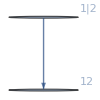

```mathematica
Graph[MobiusGraphSimple[1,allGraphs2],ImageSize->{100,100}]
```

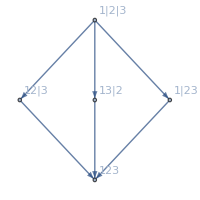

```mathematica
Graph[MobiusGraphSimple[K3Key,allGraphs3],ImageSize->{200,200}]
```

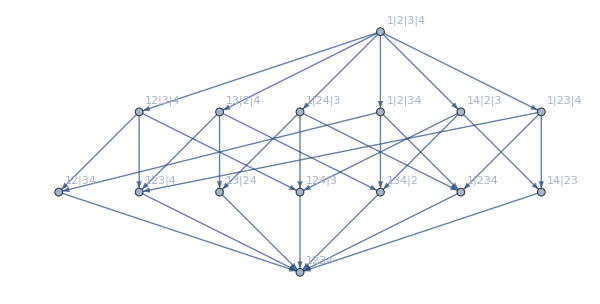

```mathematica
Graph[MobiusGraphSimple[K4Key,allGraphs4]]
```

```mathematica
MobiusGraphWithMobius[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
If[to[[1]]==n1x2x346x5,
Print[{"IsRefinement",from[[2]],to[[2]]}]
];
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Column[{StringReplace[StringDrop[SymbolName[n ],1],"x"->"|"],Style[Coefficient[form,n],Bold,Red]}],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

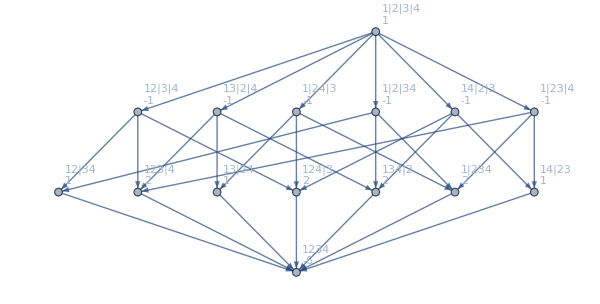

```mathematica
MobiusGraphWithMobius[K4Key,allGraphs4]
```

## Bond lattice

```mathematica
DirectedEdge
```

DirectedEdge

```mathematica
Descendents[g_,vertices_]:=Block[{result={},nodes,edges,current},
nodes=vertices;
While[nodes≠{},
current=First[nodes];
nodes=Rest[nodes];
edges=Select[EdgeList[g],#[[1]]==current&];
result=Join[result,edges];
nodes=DeleteDuplicates[Join[nodes,Map[#[[2]]&,edges]]];
];
DeleteDuplicates[result]
]
```

```mathematica
CalcSubGraph[g_,inf_, allGraphs_]:=Block[{involved={}, current={inf},result={}, values},
result={inf};
current=Map[#[[1]]&,Select[EdgeList[g],MemberQ[current,#[[2]]]&]];
While[current≠{},
result=Join[result,current];
current=Map[#[[1]]&,Select[EdgeList[g],MemberQ[current,#[[2]]]&]];
];
result=Sort[DeleteDuplicates[result]];
values=Select[Keys[allGraphs],Sort[ListofVars[allGraphs[#,"colofourrealnull"]]]==result&];
If[Length[values]>1,
Print[values];
Interrupt[]
];
First[values]
]
```

```mathematica
ChangeSymbol[s_]:=Symbol[StringReplace[SymbolName[s],"v"->"n"]]
```

```mathematica
BondLattice[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs4[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans, bondGraphs, sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs4[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
Graph[sublattice,VertexLabels->Table[n->Placed[Tooltip[
TableForm[
Framed[Graph[bondGraphs[n],VertexLabels->{1->"",2->"",3->"",4->""} ],Background->White],TableAlignments->Center],
TableForm[
{found[n,"graph"],bondGraphs[n]}]],{Center}
],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Join[
Map[#->{Thick,Darker[Green]}&,Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&]],
Map[#->{Thick,Blue}&,edges2]
],
ImageSize->300]
]
```

```mathematica
allGraphs4[271,"graph"]
```

-Graphics-

```mathematica
BondLattice[271,271,allGraphs4]
```

-Graphics-

```mathematica
BondLattice2[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs4[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans, bondGraphs, sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs4[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
Graph[sublattice,VertexLabels->Table[n->Placed[Tooltip[
TableForm[
With [{baseList=
{
Style[Coefficient[form2,n],Bold,If[Coefficient[form2,n]==0,Blue,Red]]
}},
If[KeyExistsQ[bondGraphs,n],
Join[baseList,{Framed[bondGraphs[n],Background->White]}],
baseList
]
],TableAlignments->Center],
TableForm[
{found[n,"graph"],bondGraphs[n]}]],{Center}
],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Join[
Map[#->{Thick,Darker[Green]}&,Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&]],
Map[#->{Thick,Blue}&,edges2]
],ImageSize->300]
]
```

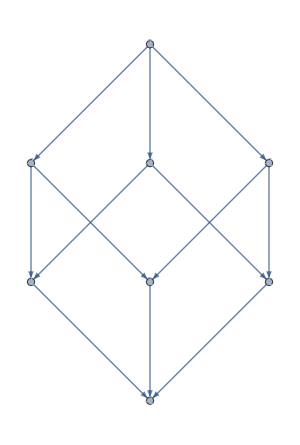

```mathematica
BondLattice2[271,271,allGraphs4]
```

```mathematica
ChromaticPolynomial[allGraphs4[271,"graph"],x]
```

-x+3 x^2-3 x^3+x^4

```mathematica
BondLattice3[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs4[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans, bondGraphs, sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs4[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
Graph[sublattice,VertexLabels->Table[n->Placed[Tooltip[
TableForm[
With [{baseList=
{
Style[StringReplace[StringDrop[SymbolName[n ],1],"x"->"|"],12,"Calibri",Black],
Style[Coefficient[form2,n],Bold,If[Coefficient[form2,n]==0,Blue,Red]]
}},
If[KeyExistsQ[bondGraphs,n],
Join[baseList,{Framed[bondGraphs[n],Background->Transparent]}],
baseList
]
],TableAlignments->Center],
TableForm[
{found[n,"graph"],bondGraphs[n]}]],{Left}
],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Join[
Map[#->{Thick,Darker[Green]}&,Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&]],
Map[#->{Thick,Blue}&,edges2]
]]
]
```

## Explaining the bond graph procedure inside the partition lattice:

```mathematica
g23=MobiusGraphSimple[K4Key,allGraphs4]
```

-Graphics-

```mathematica
Map[#[[2]]->#[[1]]&,{n14x2x3->n1x2x3x4,n12x3x4->n1x2x3x4,n1x2x34->n1x2x3x4}]
```

{n1x2x3x4->n14x2x3,n1x2x3x4->n12x3x4,n1x2x3x4->n1x2x34}

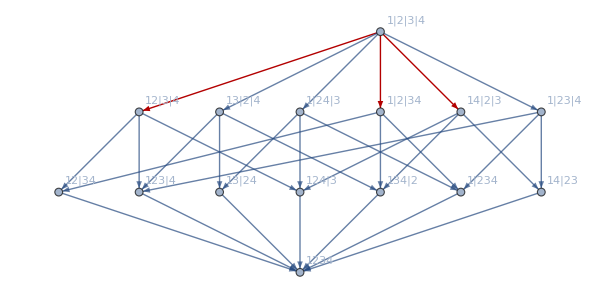

```mathematica
Graph[g23,GraphHighlight->{n1x2x3x4->n14x2x3,n1x2x3x4->n12x3x4,n1x2x3x4->n1x2x34}, GraphHighlightStyle->"Thick"]
```

```mathematica
SummaryPrint[271]
```

SummaryPrint[271]

```mathematica
Map[#[[2]]->#[[1]]&,{n14x2x3->n1x2x3x4,n12x3x4->n1x2x3x4,n1x2x34->n1x2x3x4,n12x34->n12x3x4,n12x34->n1x2x34,
n124x3->n12x3x4,n124x3->n14x2x3,n134x2->n14x2x3,n134x2->n1x2x34}]
```

{n1x2x3x4->n14x2x3,n1x2x3x4->n12x3x4,n1x2x3x4->n1x2x34,n12x3x4->n12x34,n1x2x34->n12x34,n12x3x4->n124x3,n14x2x3->n124x3,n14x2x3->n134x2,n1x2x34->n134x2}

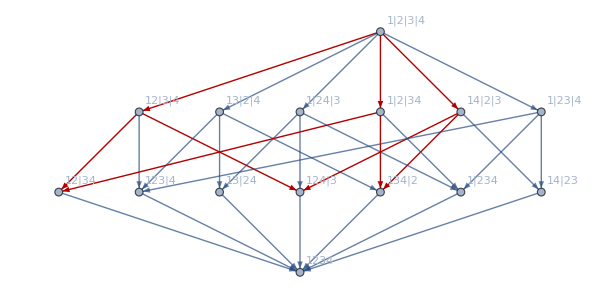

```mathematica
Graph[g23,GraphHighlight->{n1x2x3x4->n14x2x3,n1x2x3x4->n12x3x4,n1x2x3x4->n1x2x34,n12x3x4->n12x34,n1x2x34->n12x34,n12x3x4->n124x3,n14x2x3->n124x3,n14x2x3->n134x2,n1x2x34->n134x2}, GraphHighlightStyle->"Thick"]
```

```mathematica
Map[#[[2]]->#[[1]]&,{n14x2x3->n1x2x3x4,n12x3x4->n1x2x3x4,n1x2x34->n1x2x3x4,n12x34->n12x3x4,n12x34->n1x2x34,
n124x3->n12x3x4,n124x3->n14x2x3,n134x2->n14x2x3,n134x2->n1x2x34,n1234->n124x3,n1234->n134x2,n1234->n12x34}]
```

{n1x2x3x4->n14x2x3,n1x2x3x4->n12x3x4,n1x2x3x4->n1x2x34,n12x3x4->n12x34,n1x2x34->n12x34,n12x3x4->n124x3,n14x2x3->n124x3,n14x2x3->n134x2,n1x2x34->n134x2,n124x3->n1234,n134x2->n1234,n12x34->n1234}

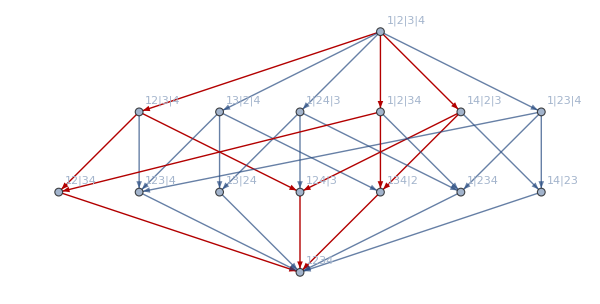

```mathematica
Graph[g23,GraphHighlight->{n1x2x3x4->n14x2x3,n1x2x3x4->n12x3x4,n1x2x3x4->n1x2x34,n12x3x4->n12x34,n1x2x34->n12x34,n12x3x4->n124x3,n14x2x3->n124x3,n14x2x3->n134x2,n1x2x34->n134x2,n124x3->n1234,n134x2->n1234,n12x34->n1234}, GraphHighlightStyle->"Thick"]
```

```mathematica
EdgeList[g23]
```

{n12x34->n1234,n13x24->n1234,n14x23->n1234,n123x4->n1234,n124x3->n1234,n134x2->n1234,n1x234->n1234,n12x3x4->n12x34,n1x2x34->n12x34,n13x2x4->n13x24,n1x24x3->n13x24,n14x2x3->n14x23,n1x23x4->n14x23,n12x3x4->n123x4,n13x2x4->n123x4,n1x23x4->n123x4,n12x3x4->n124x3,n14x2x3->n124x3,n1x24x3->n124x3,n13x2x4->n134x2,n14x2x3->n134x2,n1x2x34->n134x2,n1x23x4->n1x234,n1x24x3->n1x234,n1x2x34->n1x234,n1x2x3x4->n12x3x4,n1x2x3x4->n13x2x4,n1x2x3x4->n14x2x3,n1x2x3x4->n1x23x4,n1x2x3x4->n1x24x3,n1x2x3x4->n1x2x34}

```mathematica
BondLattice3[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs4[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans, bondGraphs, sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs4[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
Graph[sublattice,VertexLabels->Table[n->Placed[TableForm[
With [{baseList=
{
Style[StringReplace[StringDrop[SymbolName[n ],1],"x"->"|"],12,"Calibri",Black]
}},
If[KeyExistsQ[bondGraphs,n],
Join[baseList,{Framed[found[n,"graph"],Background->Transparent]}],
baseList
]
],TableAlignments->Center],{Left}
],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Join[
Map[#->{Thick,Darker[Green]}&,Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&]],
Map[#->{Thick,Blue}&,edges2]
],
ImageSize->720]
]
```

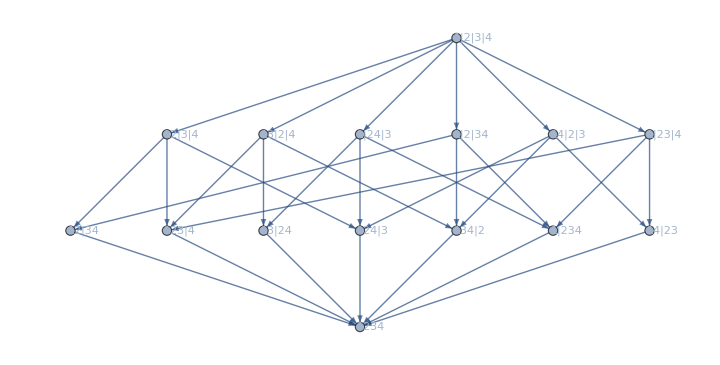

```mathematica
BondLattice3[K4Key,K4Key,allGraphs4]
```

```mathematica
BondLattice4[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs4[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans, bondGraphs, sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs4[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
Graph[sublattice,VertexLabels->Table[n->Placed[TableForm[
With [{baseList=
{
Style[StringReplace[StringDrop[SymbolName[n ],1],"x"->"|"],12,"Calibri",Black]
}},
If[KeyExistsQ[bondGraphs,n],
Join[baseList,{Framed[found[n,"graph"],Background->Transparent]}],
baseList
]
],TableAlignments->Center],{Left}
],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Join[
Map[#->{Thick,Darker[Green]}&,Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&]],
Map[#->{Thick,Blue}&,edges2]
]]
]
```

```mathematica
vl=VertexList[Graph[{n14x2x3->n1x2x3x4,n12x3x4->n1x2x3x4,n1x2x34->n1x2x3x4,n12x34->n12x3x4,n12x34->n1x2x34,
n124x3->n12x3x4,n124x3->n14x2x3,n134x2->n14x2x3,n134x2->n1x2x34,n1234->n124x3,n1234->n134x2,n1234->n12x34}]]
```

{n14x2x3,n1x2x3x4,n12x3x4,n1x2x34,n12x34,n124x3,n134x2,n1234}

```mathematica
labels=Table[v->
Placed[
Column[{
StringReplace[StringDrop[SymbolName[v ],1],"x"->"|"],
Framed[(v/.repBase4NullBare), Background->White],
Style[Coefficient[allGraphs4[271,"colofourrealnull"],v],Bold,Darker[Green]]
}, Center
], {Center}], {v,vl}]
```

{n14x2x3→Placed[14|2|3
-Graphics-
-1,{Center}],n1x2x3x4→Placed[1|2|3|4
-Graphics-
1,{Center}],n12x3x4→Placed[12|3|4
-Graphics-
-1,{Center}],n1x2x34→Placed[1|2|34
-Graphics-
-1,{Center}],n12x34→Placed[12|34
-Graphics-
1,{Center}],n124x3→Placed[124|3
-Graphics-
1,{Center}],n134x2→Placed[134|2
-Graphics-
1,{Center}],n1234→Placed[1234
-Graphics-
-1,{Center}]}

```mathematica
Map[#[[2]]->#[[1]]&,{n14x2x3->n1x2x3x4,n12x3x4->n1x2x3x4,n1x2x34->n1x2x3x4,n12x34->n12x3x4,n12x34->n1x2x34,
n124x3->n12x3x4,n124x3->n14x2x3,n134x2->n14x2x3,n134x2->n1x2x34,n1234->n124x3,n1234->n134x2,n1234->n12x34}]
```

{n1x2x3x4->n14x2x3,n1x2x3x4->n12x3x4,n1x2x3x4->n1x2x34,n12x3x4->n12x34,n1x2x34->n12x34,n12x3x4->n124x3,n14x2x3->n124x3,n14x2x3->n134x2,n1x2x34->n134x2,n124x3->n1234,n134x2->n1234,n12x34->n1234}

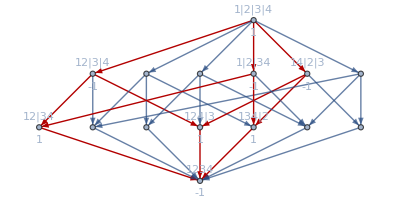

```mathematica
Graph[VertexList[g23],EdgeList[g23],GraphHighlight->{n1x2x3x4->n14x2x3,n1x2x3x4->n12x3x4,n1x2x3x4->n1x2x34,n12x3x4->n12x34,n1x2x34->n12x34,n12x3x4->n124x3,n14x2x3->n124x3,n14x2x3->n134x2,n1x2x34->n134x2,n124x3->n1234,n134x2->n1234,n12x34->n1234},GraphHighlightStyle->"Thick",  VertexLabels->labels]
```

```mathematica
allGraphs4[271,"colofourrealnull"]/.repBase4NullBare
```

--Graphics-+-Graphics-+-Graphics-+-Graphics---Graphics---Graphics---Graphics-+-Graphics-

## Some bond lattice graphs

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==2&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->4]
]&]
```

{244}

```mathematica
allGraphs4[244,"graph"]
```

-Graphics-

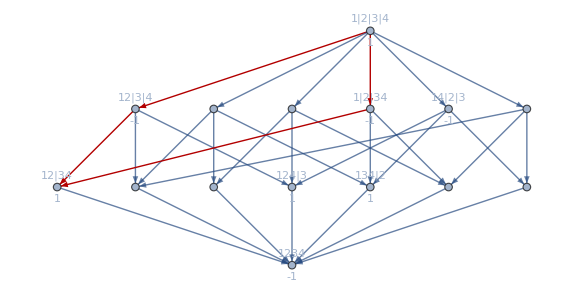

```mathematica
Graph[VertexList[g23],EdgeList[g23],GraphHighlight->EdgeList[MobiusGraph4[244,allGraphs4]],GraphHighlightStyle->"Thick",  VertexLabels->labels]
```

```mathematica
allGraphs4[244,"colofourrealnull"]/.repBase4NullBare
```

-Graphics---Graphics---Graphics-+-Graphics-

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==2&&EdgeQ[g,1<->4]&&EdgeQ[g,3<->4]
]&]
```

{28}

```mathematica
allGraphs4[28,"graph"]
```

-Graphics-

```mathematica
allGraphs4[28,"colofourrealnull"]/.repBase4NullBare
```

-Graphics---Graphics---Graphics-+-Graphics-

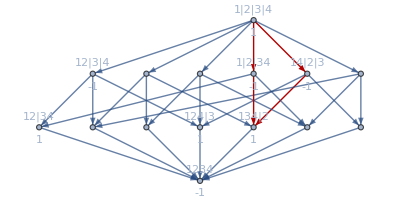

```mathematica
Graph[VertexList[g23],EdgeList[g23],GraphHighlight->EdgeList[MobiusGraph4[28,allGraphs4]],GraphHighlightStyle->"Thick",  VertexLabels->labels]
```

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==1&&EdgeQ[g,1<->4]
]&]
```

{27}

```mathematica
allGraphs4[27,"graph"]
```

-Graphics-

```mathematica
allGraphs4[27,"colofourrealnull"]/.repBase4NullBare
```

--Graphics-+-Graphics-

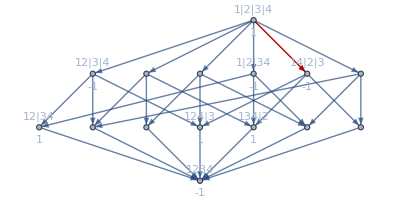

```mathematica
Graph[VertexList[g23],EdgeList[g23],GraphHighlight->EdgeList[MobiusGraph4[27,allGraphs4]],GraphHighlightStyle->"Thick",  VertexLabels->labels]
```

## More examples

```mathematica
RandomSample[ Keys[allGraphs4],5]
```

{367,243,30,666,417}

```mathematica
MobiusGraphDouble44[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs4[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans, bondGraphs, sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs4[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
Graph[vars,edges,VertexLabels->Table[n->Placed[Tooltip[
TableForm[
With [{baseList=
{
Style[n,12,"Calibri",If[Coefficient[form3,n]==0,Black,Blue]],
Style[Coefficient[form2,n],Bold,If[Coefficient[form2,n]==0,Blue,Red]]
}},
If[KeyExistsQ[bondGraphs,n],
Join[baseList,{Framed[found[n,"graph"],Background->Transparent]}],
baseList
]
],TableAlignments->Center],
TableForm[
{found[n,"graph"],bondGraphs[n]}]],{Left}
],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",

GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
GraphHighlightStyle->"Thick",
ImageSize->500]
]
```

```mathematica
SummaryPrint44[k_]:=With[
{g=MobiusGraphDouble44[K4Key,k,allGraphs4], gr=allGraphs4[k,"graph"]},
Framed[
Labeled[
Row[{
Labeled[Graph[gr,ImageSize->{40,40}],Style[k,Bold,12, Underlined,Red]],
Rotate[g,Pi/2]
}],
{Style[StandardForm[allGraphs4[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],
Framed[Style[StandardForm[((allGraphs4[k,"colofour"])/.repBase4)],Darker[Green],12]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

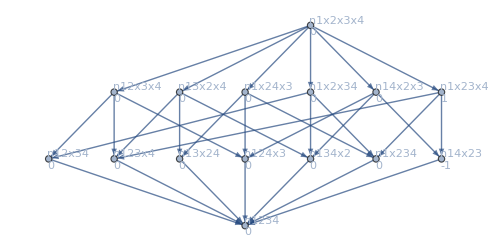
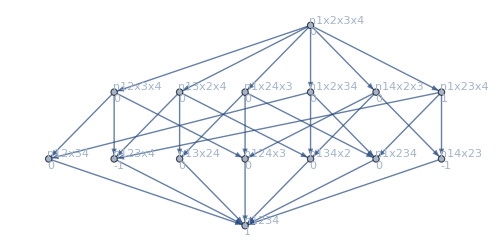
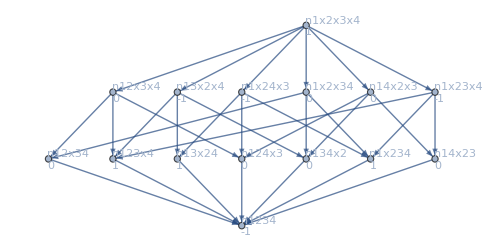
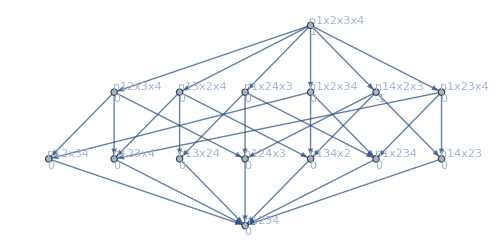
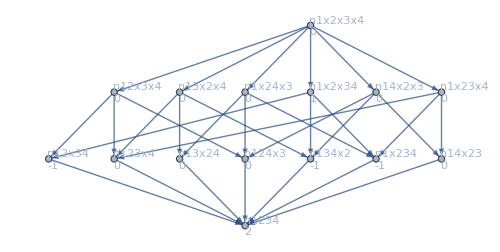
{-Graphics-45-Graphics--n14x23+n1x23x4x^3-x^2
(x-1) x^2
-Graphics-+-Graphics-+-Graphics-,-Graphics-369-Graphics-n1234-n123x4-n14x23+n1x23x4x^3-2 x^2+x
(x-1)^2 x
-Graphics-+-Graphics-,-Graphics-93-Graphics--n1234+n123x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4x^4-3 x^3+3 x^2-x
(x-1)^3 x
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-27-Graphics--n14x2x3+n1x2x3x4x^4-x^3
(x-1) x^3
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-365-Graphics-2 n1234-n12x34-n134x2-n1x234+n1x2x34x^3-3 x^2+2 x
(x-2) (x-1) x
-Graphics-}

```mathematica
Table[
SummaryPrint44[k]
,{k,{45,369,93,27,365}}
]
```

## Vertex partition illustrations

```mathematica
allGraphs5[0,"graph"]
```

-Graphics-

```mathematica
Table[allGraphs5[k,"graph"],{k,Flatten[allGraphs5[0,"children"]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Vertex partitions

```mathematica
Map[StringReplace[StringDrop[SymbolName[#],1],"x"->"|"]&,ListofVars[allGraphs4[271,"colofour"]]]
```

{13|24,13|2|4,1|23|4,1|24|3,1|2|3|4}

```mathematica
Map[StringReplace[StringDrop[SymbolName[#],1],"x"->"|"]&,ListofVars[allGraphs4[271,"colofourrealnull"]]]
```

{124|3,12|34,134|2,1|2|3|4,1234,12|3|4,14|2|3,1|2|34}

## Partition graphs adding green

```mathematica
DescendentsGreen[g_,vertices_]:=Block[{result={},nodes,edges,current},
nodes=vertices;
While[nodes≠{},
current=First[nodes];
nodes=Rest[nodes];
edges=Select[EdgeList[g],#[[1]]==current&];
result=Join[result,edges];
nodes=Join[nodes,Map[#[[2]]&,edges]];
];
result
]
```

```mathematica
MobiusGraphDoubleGreen[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs[key2,"colofour"]],
pairs, 
vars, 
blocks=Association[],
c,
edges,
edges2,
set, 
found=Association[],
mob,
realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],
nonRoot,
edgesTrans,
 bondGraphs,
 sublattice},

vars=ListofVars[form];
Table[blocks[k]={},{k,0,6}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,6}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=DescendentsGreen[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
Graph[vars,edges,VertexLabels->Table[n->StringReplace[StringDrop[SymbolName[n],1],"x"->"|"],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Join[
Map[#->{Thick,Darker[Green]}&,Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&]]
],
VertexStyle->Map[#->Darker[Green]&,VertexList[Graph[edgesTrans]]],
GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
GraphHighlightStyle->"Thick",
ImageSize->720]
]
```

```mathematica
SummaryPrintGreen[k_]:=With[
{g=MobiusGraphDoubleGreen[K4Key,k,allGraphs4], gr=allGraphs4[k,"graph"]},
g
]
```

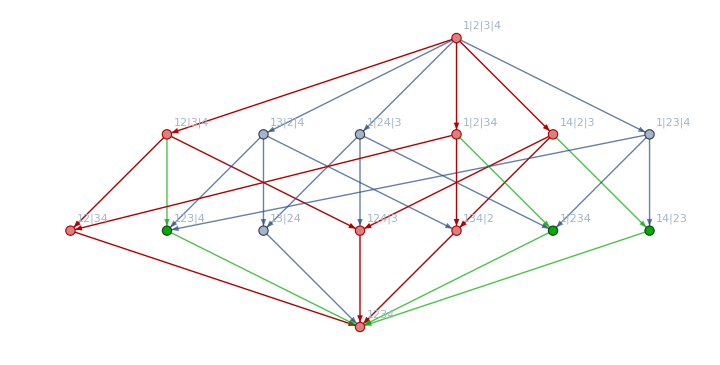

```mathematica
SummaryPrintGreen[271]
```

```mathematica
Table[Length[ListofVars[allGraphs4[k,"colofour"]]]+Length[ListofVars[allGraphs4[k,"colofourrealnull"]]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]//Tally//Sort
```

{{9,4},{11,15},{12,6},{13,28},{15,6},{16,5}}

```mathematica
Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]
```

{0,243,324,351,360,363,364,361,354,355,352,333,336,337,334,327,328,325,270,279,282,283,280,273,274,271,252,255,256,253,246,247,244,81,108,117,120,121,118,111,112,109,90,93,94,91,84,85,82,27,36,39,40,37,30,31,28,9,12,13,10,3,4,1}

## Both formulas inside same lattice graph

```mathematica
MobiusGraphDoubleGood[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans, bondGraphs, sublattice},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
Graph[vars,edges,VertexLabels->Table[n->StringReplace[StringDrop[SymbolName[n],1],"x"->"|"],{n,vars}],GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Join[
Map[#->{Thick,Darker[Green]}&,Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&]],
Map[#->{Thick,Blue}&,edges2]
],
GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
GraphHighlightStyle->"Thick",
ImageSize->720]
]
```

```mathematica
SummaryPrintGood[k_]:=With[
{g=MobiusGraphDoubleGood[K4Key,k,allGraphs4], gr=allGraphs4[k,"graph"]},
Framed[
Labeled[
Row[{
Labeled[Graph[gr,ImageSize->{40,40}],Style[k,Bold,12, Underlined,Red]],
g
}],
{Style[StandardForm[allGraphs4[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Row[Table[Style[ChromaticPolynomial[gr,m],Blue],{m,1,5}], " * "],
Framed[Style[StandardForm[((allGraphs4[k,"colofour"])/.repBase4)],Darker[Green],12]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

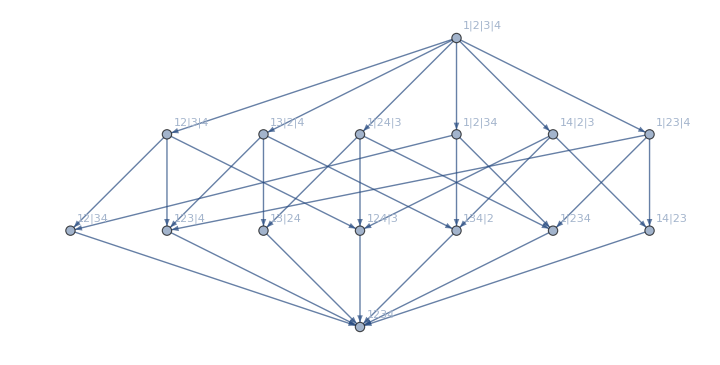
-Graphics-271-Graphics--n1234+n124x3+n12x34-n12x3x4+n134x2-n14x2x3-n1x2x34+n1x2x3x4x^4-3 x^3+3 x^2-x
(x-1)^3 x
 *  * 0224108320
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood[271]
```

## Empty graph in full base and vice versa.

```mathematica
allGraphs4[0,"graph"]
```

-Graphics-

```mathematica
allGraphs4[0,"colofour"]/.repBase4Bare
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
allGraphs4[K4Key,"graph"]
```

-Graphics-

```mathematica
repBase4NullBareBoxed=Table[allGraphs4[k,"colofourrealnull"]->Framed[allGraphs4[k,"graph"]],{k,allGraphs4NullAtomKeys}]
```

{n1x2x3x4→-Graphics-,n12x3x4→-Graphics-,n123x4→-Graphics-,n1234→-Graphics-,n124x3→-Graphics-,n12x34→-Graphics-,n13x2x4→-Graphics-,n134x2→-Graphics-,n13x24→-Graphics-,n14x2x3→-Graphics-,n14x23→-Graphics-,n1x23x4→-Graphics-,n1x234→-Graphics-,n1x24x3→-Graphics-,n1x2x34→-Graphics-}

```mathematica
allGraphs4[K4Key,"colofourrealnull"]/.repBase4NullBareBoxed
```

-6 -Graphics-+2 -Graphics-+2 -Graphics-+-Graphics-+2 -Graphics-+-Graphics-+2 -Graphics-+-Graphics---Graphics---Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics-

```mathematica
TableForm[Table[allGraphs4[k,"graph"],{k,Select[Keys[allGraphs4],IsomorphicGraphQ[allGraphs4[#,"graph"],CompleteGraph[3]]&]}], TableDirections->Row]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Deletion contraction tree for additive procedure

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==3&&EdgeCount[g]==3]&]}]
```

{-Graphics-365,-Graphics-367,-Graphics-373,-Graphics-391,-Graphics-445,-Graphics-607}

```mathematica
Graph[Table[Framed[allGraphs4[e[[1]],"graph"],Background->White]->Framed[allGraphs4[e[[2]],"graph"],Background->White],{e,{{271,442},{271,352},{442,448},{442,445},{352,373},{352,361},{361,367},{361,364}}}], VertexLabels->{"Name"}]
```

-Graphics-

## Deletion contraction tree for subtractive procedure

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==0]&]}]
```

{-Graphics-0}

```mathematica
Graph[Table[Framed[allGraphs4[e[[1]],"graph"],Background->White]->Framed[allGraphs4[e[[2]],"graph"],Background->White],{e,{{271,517},{271,28},{517,637},{517,487},{637,728},{637,546},{487,488},{487,486},{28,110},{28,27},{110,218},{110,2},{27,54},{27,0}}}], VertexLabels->{"Name"}]
```

-Graphics-

## Sublattices and so

```mathematica
MobiusGraphSublattices[key_,subKey_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]],subGraph=MobiusGraph4[subKey,allGraphs]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[
vars,
edges,
VertexLabels->Table[n->StringReplace[StringDrop[SymbolName[n ],1],"x"->"|"],{n,vars}],
GraphHighlight->Join[EdgeList[subGraph],VertexList[subGraph]],
ImageSize->150,
GraphLayout->"LayeredDigraphEmbedding"]
]
```

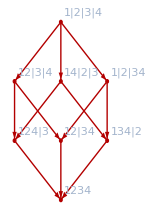

```mathematica
MobiusGraphSublattices[271,271,allGraphs4]
```

```mathematica
empties=Sort[DeleteDuplicates[Flatten[{{271,517},{271,28},{517,637},{517,487},{637,728},{637,546},{487,488},{487,486},{28,110},{28,27},{110,218},{110,2},{27,54},{27,0}}]]]
```

{0,2,27,28,54,110,218,271,486,487,488,517,546,637,728}

```mathematica
Subsets[EdgeList[allGraphs4[271,"graph"]]]
```

{{},{1<->2},{1<->4},{3<->4},{1<->2,1<->4},{1<->2,3<->4},{1<->4,3<->4},{1<->2,1<->4,3<->4}}

```mathematica
Table[s->Select[Keys[allGraphs4],
With[{g=allGraphs4[#,"graph"]},
EdgeCount[g]==Length[s]&& EdgeList[g]==EdgeList[ Subgraph[allGraphs4[271,"graph"],s]]&&VertexCount[g]==4]
&],{s, Subsets[EdgeList[allGraphs4[271,"graph"]]]}]
```

{{}→{0},{1<->2}→{243},{1<->4}→{27},{3<->4}→{1},{1<->2,1<->4}→{270},{1<->2,3<->4}→{},{1<->4,3<->4}→{28},{1<->2,1<->4,3<->4}→{271}}

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},
EdgeCount[g]==2&&VertexCount[g]==4 && EdgeQ[g,1<->2]&& EdgeQ[g,3<->4]]
&
]
```

{244}

```mathematica
Select[Keys[allGraphs4],
With[{g=allGraphs4[#,"graph"]},
 EdgeList[g]==EdgeList[ Subgraph[allGraphs4[271,"graph"],s]]&&VertexCount[g]==4]
&]
```

{0}

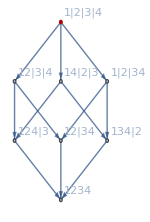
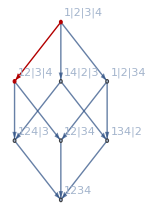
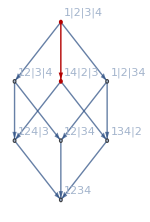
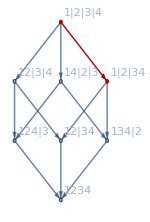
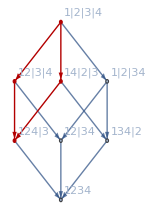
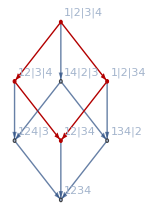
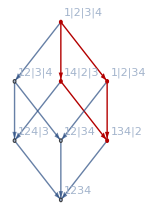
{-Graphics-0→-Graphics-,-Graphics-243→-Graphics-,-Graphics-27→-Graphics-,-Graphics-1→-Graphics-,-Graphics-270→-Graphics-,-Graphics-244→-Graphics-,-Graphics-28→-Graphics-,-Graphics-271→-Graphics-}

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k]->MobiusGraphSublattices[271,k,allGraphs4],{k,Sort[DeleteDuplicates[Flatten[{{{0},{243},{27},{1},{270},{244},{28},{271}}}]],
Smaller[VertexCount[allGraphs4[#1,"graph"]],VertexCount[allGraphs4[#2,"graph"]]]&]}]
```

```mathematica
Sublattices and so level 2
```

2 and level so Sublattices

```mathematica
Select[Keys[allGraphs4],allGraphs4[#,"vertexsets"]=={{1,2},{3},{4}} 
&
]
```

{486,576,606,607,577,516,517,487}

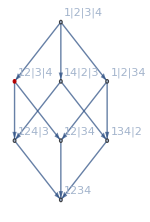
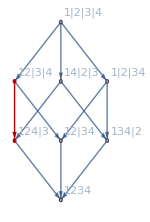
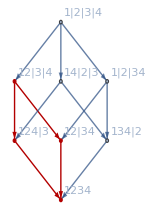
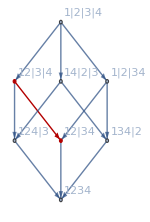
{-Graphics-→-Graphics-,-Graphics-→Graph[{n124x3,n12x34,n134x2,n1x2x3x4,n1234,n12x3x4,n14x2x3,n1x2x34},{n124x3->n1234,n12x34->n1234,n134x2->n1234,n12x3x4->n124x3,n14x2x3->n124x3,n12x3x4->n12x34,n1x2x34->n12x34,n14x2x3->n134x2,n1x2x34->n134x2,n1x2x3x4->n12x3x4,n1x2x3x4->n14x2x3,n1x2x3x4->n1x2x34},VertexLabels→{n124x3→124|3,n12x34→12|34,n134x2→134|2,n1x2x3x4→1|2|3|4,n1234→1234,n12x3x4→12|3|4,n14x2x3→14|2|3,n1x2x34→1|2|34},GraphHighlight→{n12x3x4->n123x4,n12x3x4,n123x4},ImageSize→150,GraphLayout→LayeredDigraphEmbedding],-Graphics-→Graph[{n124x3,n12x34,n134x2,n1x2x3x4,n1234,n12x3x4,n14x2x3,n1x2x34},{n124x3->n1234,n12x34->n1234,n134x2->n1234,n12x3x4->n124x3,n14x2x3->n124x3,n12x3x4->n12x34,n1x2x34->n12x34,n14x2x3->n134x2,n1x2x34->n134x2,n1x2x3x4->n12x3x4,n1x2x3x4->n14x2x3,n1x2x3x4->n1x2x34},VertexLabels→{n124x3→124|3,n12x34→12|34,n134x2→134|2,n1x2x3x4→1|2|3|4,n1234→1234,n12x3x4→12|3|4,n14x2x3→14|2|3,n1x2x34→1|2|34},GraphHighlight→{n123x4->n1234,n124x3->n1234,n12x3x4->n123x4,n12x3x4->n124x3,n1234,n12x3x4,n123x4,n124x3},ImageSize→150,GraphLayout→LayeredDigraphEmbedding],-Graphics-→Graph[{n124x3,n12x34,n134x2,n1x2x3x4,n1234,n12x3x4,n14x2x3,n1x2x34},{n124x3->n1234,n12x34->n1234,n134x2->n1234,n12x3x4->n124x3,n14x2x3->n124x3,n12x3x4->n12x34,n1x2x34->n12x34,n14x2x3->n134x2,n1x2x34->n134x2,n1x2x3x4->n12x3x4,n1x2x3x4->n14x2x3,n1x2x3x4->n1x2x34},VertexLabels→{n124x3→124|3,n12x34→12|34,n134x2→134|2,n1x2x3x4→1|2|3|4,n1234→1234,n12x3x4→12|3|4,n14x2x3→14|2|3,n1x2x34→1|2|34},GraphHighlight→{n123x4->n1234,n124x3->n1234,n12x34->n1234,n12x3x4->n123x4,n12x3x4->n124x3,n12x3x4->n12x34,n12x3x4,n1234,n123x4,n124x3,n12x34},ImageSize→150,GraphLayout→LayeredDigraphEmbedding],-Graphics-→Graph[{n124x3,n12x34,n134x2,n1x2x3x4,n1234,n12x3x4,n14x2x3,n1x2x34},{n124x3->n1234,n12x34->n1234,n134x2->n1234,n12x3x4->n124x3,n14x2x3->n124x3,n12x3x4->n12x34,n1x2x34->n12x34,n14x2x3->n134x2,n1x2x34->n134x2,n1x2x3x4->n12x3x4,n1x2x3x4->n14x2x3,n1x2x3x4->n1x2x34},VertexLabels→{n124x3→124|3,n12x34→12|34,n134x2→134|2,n1x2x3x4→1|2|3|4,n1234→1234,n12x3x4→12|3|4,n14x2x3→14|2|3,n1x2x34→1|2|34},GraphHighlight→{n123x4->n1234,n12x34->n1234,n12x3x4->n123x4,n12x3x4->n12x34,n1234,n12x3x4,n123x4,n12x34},ImageSize→150,GraphLayout→LayeredDigraphEmbedding],-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}

```mathematica
Table[allGraphs4[k,"graph"]->MobiusGraphSublattices[271,k,allGraphs4],{k,Sort[DeleteDuplicates[Flatten[{486,576,606,607,577,516,517,487}]],
Smaller[VertexCount[allGraphs4[#1,"graph"]],VertexCount[allGraphs4[#2,"graph"]]]&]}]
```

```mathematica
Sublattices and so level 2
```

2 and level so Sublattices

```mathematica
Select[Keys[allGraphs4],allGraphs4[#,"vertexsets"]=={{1,2,4},{3}} 
&
]
```

{637,546}

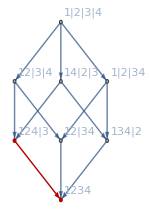
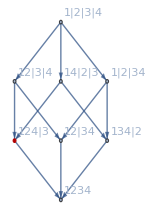
{-Graphics-→-Graphics-,-Graphics-→-Graphics-}

```mathematica
Table[allGraphs4[k,"graph"]->MobiusGraphSublattices[271,k,allGraphs4],{k,{637,546}}]
```

```mathematica
Sum[StirlingS2[4,k+1]2^((k(k-1))/2),{k,3,1,-1}]
```

27

```mathematica
StirlingS2[4,3]
```

6

```mathematica
With[{k=4},2^((k(k-1))/2)]
```

64

```mathematica
1*8+3*4+3*2
```

26

## The effect of adding a vertex

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==3 && EdgeCount[g]==2]
&
]
```

{369,357,353,382,346,442,417,286,309,257,606,577,517,122,145,97,193,49}

```mathematica
EdgeList[allGraphs4[369,"graph"]]
```

{1<->2,1<->3}

```mathematica
SummaryPrintGood[369]
```

-Graphics-369-Graphics-n1234-n123x4-n14x23+n1x23x4x^3-2 x^2+x
(x-1)^2 x
 *  * 02123680
-Graphics-+-Graphics-

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4 && EdgeCount[g]==2&&EdgeQ[g,1<->2]&&EdgeQ[g,1<->4]]
&
]
```

{270}

```mathematica
N[{270}]
```

{270.}

```mathematica
SummaryPrintGood[270]
```

-Graphics-270-Graphics-n124x3-n12x3x4-n14x2x3+n1x2x3x4x^4-2 x^3+x^2
(x-1)^2 x^2
 *  * 0436144400
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

## Maximum K3 that is not K4 inside Partition Lattice of size 4

```mathematica
FindClique[allGraphs4[K4Key,"graph"],{4}]!={}
```

True

```mathematica
Map[{#,EdgeCount[allGraphs5[#,"graph"]]}&,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},Greater[EdgeCount[g],7]&&VertexCount[g]==5&&FindClique[g,{4}]=={}&& FindClique[g,{3}]!={}]&]]
```

{{29488,8},{29440,8},{29280,8},{28786,8},{28714,8},{28552,8},{27334,8},{27310,8},{27094,8},{22962,8},{22936,8},{22882,8},{9840,8},{9838,8},{9832,8}}

```mathematica
allGraphs5[29520,"graph"]
```

-Graphics-

```mathematica
rep5=Table[allGraphs5[k,"colofour"]->allGraphs5[k,"graph"],{k,allGraphs5AtomKeys}];
```

```mathematica
rep4=Table[allGraphs4[k,"colofour"]->allGraphs4[k,"graph"],{k,allGraphs4AtomKeys}];
```

```mathematica
MobiusGraphDoubleGood5[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans, bondGraphs, sublattice,greenEdges,greenVertices, blueEdges, blueVertices},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
sublattice=mob;
bondGraphs=Association[Map[#->allGraphs[ CalcSubGraph[sublattice,#,allGraphs],"graph"]&,VertexList[sublattice]]];
greenEdges=Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&];
greenVertices=Map[#[[2]]&,greenEdges];
blueEdges=edges2;
blueVertices=Map[#[[2]]&,blueEdges];
Graph[vars,edges,
VertexLabels->Table[n->Rotate[StringReplace[StringDrop[SymbolName[n],1],"x"->"|"],Pi/4],{n,vars}],
GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Join[
Map[#->{Darker[Green]}&,greenEdges],
Map[#->{Blue}&,edges2]
],
VertexStyle->Join[Map[#->Darker[Green]&,greenVertices],Map[#->Darker[Blue]&,blueVertices]],
GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
ImageSize->720]
]
```

```mathematica
SummaryPrintGood5[k_]:=Block[
{g=MobiusGraphDoubleGood5[K5Key,k,allGraphs5], gr=allGraphs5[k,"graph"],compKey=FindComplement[k,allGraphs5],comp={},g2},
comp=allGraphs5[compKey,"graph"];
g2=MobiusGraphDoubleGood5[K5Key,compKey,allGraphs5];
Framed[
Labeled[
Column[{
TableForm[{Labeled[Graph[gr,ImageSize->200],Style[k,Bold,12, Underlined,Red]],Labeled[Graph[comp,ImageSize->200],Style[compKey,Bold,12, Underlined,Red]]}, TableDirections->Row],
Graph[g,ImageSize->1800],
Graph[g2,ImageSize->1800]
},Alignment->Center],
{Style[StandardForm[allGraphs5[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Row[Table[Style[ChromaticPolynomial[gr,m],Blue],{m,1,5}], " * "],
Framed[Style[StandardForm[((allGraphs5[k,"colofour"]/.rep5))],Darker[Green],12]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

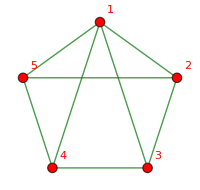
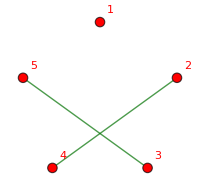
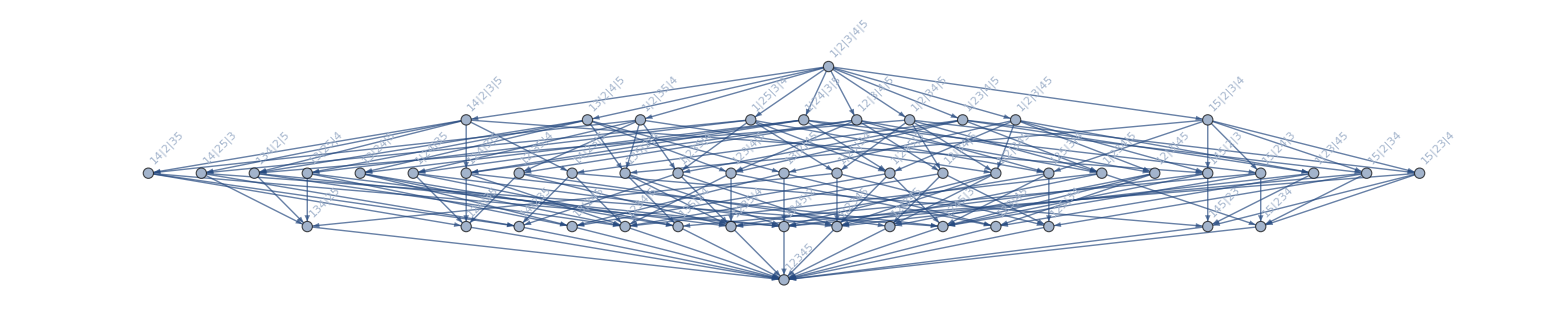
-Graphics-29440 | -Graphics-84
-Graphics-
-Graphics-14 n12345-4 n1234x5-4 n1235x4-2 n123x45+2 n123x4x5-4 n1245x3+n124x3x5-2 n125x34+2 n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-4 n1345x2-2 n134x25+2 n134x2x5+n135x2x4-n13x245+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-n14x235+n14x23x5+n14x25x3-n14x2x3x5-n15x234+n15x23x4+n15x2x34-n15x2x3x4-3 n1x2345+n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5x^5-8 x^4+24 x^3-31 x^2+14 x
(x-2) (x-1) x (x^2-5 x+7)
 *  * 00672420
-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood5[29440]
```

## Mobius matrix

```mathematica
CompareSymbols[s1_,s2_]:=Block[{str1,str2,c1,c2},
str1=StringDrop[SymbolName[s1],1];
str2=StringDrop[SymbolName[s2],1];
c1=StringCount[str1,"x"];
c2=StringCount[str2,"x"];
If[c1≠c2,
Greater[c1,c2],
str1=StringReplace[str1,"x"->"-"];
str2=StringReplace[str2,"x"->"-"];
AlphabeticOrder[ str1,str2]>0
]
]
```

```mathematica
allZeroFourSymbolsSorted=Sort[allGraphs4NullAtomKeys,CompareSymbols[allGraphs4[#1,"colofourrealnull"],allGraphs4[#2,"colofourrealnull"]]&]
```

{0,2,18,6,486,162,54,26,488,666,546,168,218,72,728}

```mathematica
Table[k->allGraphs4[k,"vertexsets"],{k,allZeroFourSymbolsSorted}]//TableForm
```

0→{{1},{2},{3},{4}}
2→{{1},{2},{3,4}}
18→{{1},{2,3},{4}}
6→{{1},{2,4},{3}}
486→{{1,2},{3},{4}}
162→{{1,3},{2},{4}}
54→{{1,4},{2},{3}}
26→{{1},{2,3,4}}
488→{{1,2},{3,4}}
666→{{1,2,3},{4}}
546→{{1,2,4},{3}}
168→{{1,3},{2,4}}
218→{{1,3,4},{2}}
72→{{1,4},{2,3}}
728→{{1,2,3,4}}

```mathematica
Table[
With[
{ibis=allZeroFourSymbolsSorted[[i]],
jbis=allZeroFourSymbolsSorted[[j]]
},
If[Greater[i,j],
0
,
If[ibis==jbis,1,
If[IsRefinement[allGraphs4[jbis,"vertexsets"],allGraphs4[ibis,"vertexsets"]],
{i,j},0]
]
]
]
,{i,15},{j,15}]//MatrixForm
```

(1 | {1,2} | {1,3} | {1,4} | {1,5} | {1,6} | {1,7} | {1,8} | {1,9} | {1,10} | {1,11} | {1,12} | {1,13} | {1,14} | {1,15}
0 | 1 | 0 | 0 | 0 | 0 | 0 | {2,8} | {2,9} | 0 | 0 | 0 | {2,13} | 0 | {2,15}
0 | 0 | 1 | 0 | 0 | 0 | 0 | {3,8} | 0 | {3,10} | 0 | 0 | 0 | {3,14} | {3,15}
0 | 0 | 0 | 1 | 0 | 0 | 0 | {4,8} | 0 | 0 | {4,11} | {4,12} | 0 | 0 | {4,15}
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | {5,9} | {5,10} | {5,11} | 0 | 0 | 0 | {5,15}
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | {6,10} | 0 | {6,12} | {6,13} | 0 | {6,15}
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | {7,11} | 0 | {7,13} | {7,14} | {7,15}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | {8,15}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | {9,15}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | {10,15}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | {11,15}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | {12,15}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | {13,15}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | {14,15}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Calculating the mobius naked

## The effect of certain operations

```mathematica
SummaryPrintGood[271]
```

-Graphics-271-Graphics--n1234+n124x3+n12x34-n12x3x4+n134x2-n14x2x3-n1x2x34+n1x2x3x4x^4-3 x^3+3 x^2-x
(x-1)^3 x
 *  * 0224108320
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],allGraphs4[#,"vertexsets"]=={{1,2},{3},{4}}&&EdgeCount[allGraphs4[#,"graph"]]==2&]}]
```

{-Graphics-606,-Graphics-577,-Graphics-517}

```mathematica
SummaryPrintGood[517]
```

-Graphics-517-Graphics-n1234-n124x3-n12x34+n12x3x4x^3-2 x^2+x
(x-1)^2 x
 *  * 02123680
-Graphics-+-Graphics-

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],allGraphs4[#,"vertexsets"]=={{1,4},{2},{3}}&&EdgeCount[allGraphs4[#,"graph"]]==2&]}]
```

{-Graphics-382,-Graphics-309,-Graphics-145}

```mathematica
SummaryPrintGood[382]
```

-Graphics-382-Graphics-n1234-n124x3-n134x2+n14x2x3x^3-2 x^2+x
(x-1)^2 x
 *  * 02123680
-Graphics-+-Graphics-

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],allGraphs4[#,"vertexsets"]=={{1},{2,3},{4}}&&EdgeCount[allGraphs4[#,"graph"]]==3&]}]
```

{-Graphics-373}

```mathematica
SummaryPrintGood[373]
```

-Graphics-373-Graphics-2 n1234-n123x4-n14x23-n1x234+n1x23x4x^3-3 x^2+2 x
(x-2) (x-1) x
 *  * 0062460
-Graphics-

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],allGraphs4[#,"vertexsets"]=={{1},{2,4},{3}}&&EdgeCount[allGraphs4[#,"graph"]]==2&]}]
```

{-Graphics-357,-Graphics-286,-Graphics-97}

```mathematica
SummaryPrintGood[286]
```

-Graphics-286-Graphics-n1234-n124x3-n1x234+n1x24x3x^3-2 x^2+x
(x-1)^2 x
 *  * 02123680
-Graphics-+-Graphics-

## The effect of adding an edge

```mathematica
allGraphs4[271,"graph"]
```

-Graphics-

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==4]&]}]
```

{-Graphics-360,-Graphics-354,-Graphics-352,-Graphics-336,-Graphics-334,-Graphics-328,-Graphics-282,-Graphics-280,-Graphics-274,-Graphics-256,-Graphics-120,-Graphics-118,-Graphics-112,-Graphics-94,-Graphics-40}

```mathematica
SummaryPrintGood[271]
```

-Graphics-271-Graphics--n1234+n124x3+n12x34-n12x3x4+n134x2-n14x2x3-n1x2x34+n1x2x3x4x^4-3 x^3+3 x^2-x
(x-1)^3 x
 *  * 0224108320
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood[280]
```

-Graphics-280-Graphics--3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4x^4-4 x^3+6 x^2-3 x
(x-1) x (x^2-3 x+3)
 *  * 021884260
-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood[274]
```

-Graphics-274-Graphics--2 n1234+2 n124x3+n12x34-n12x3x4+n134x2-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4x^4-4 x^3+5 x^2-2 x
(x-2) (x-1)^2 x
 *  * 001272240
-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood[352]
```

-Graphics-352-Graphics--2 n1234+n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4-n14x2x3-n1x2x34+n1x2x3x4x^4-4 x^3+5 x^2-2 x
(x-2) (x-1)^2 x
 *  * 001272240
-Graphics-+-Graphics-+-Graphics-

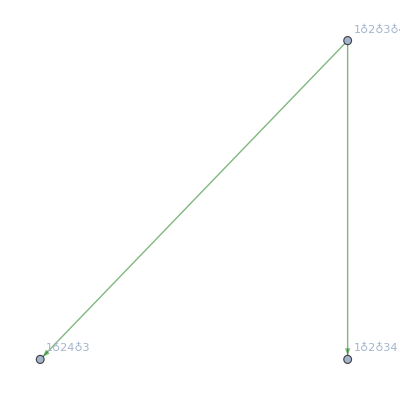
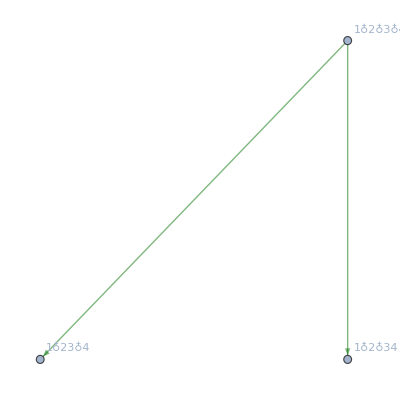
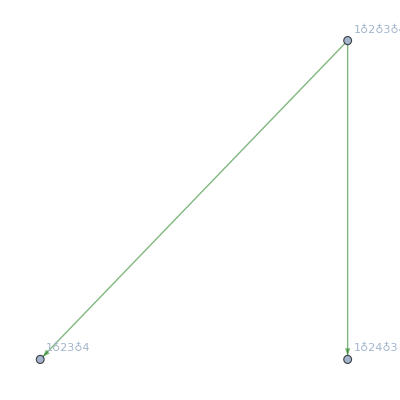
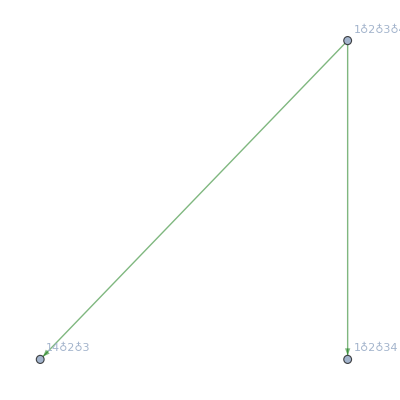
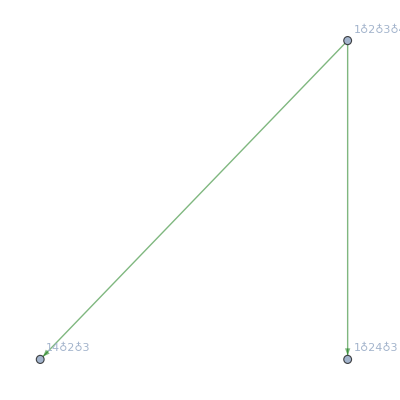
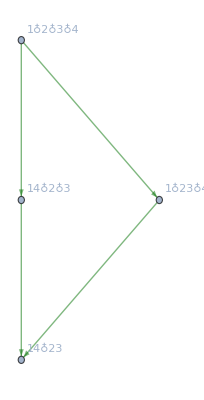
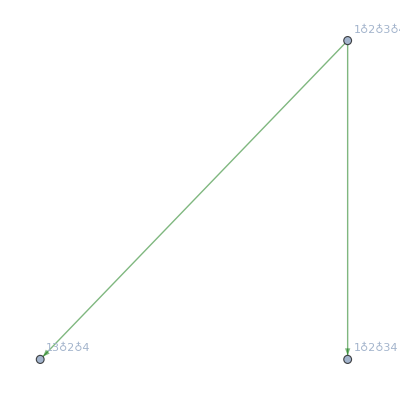
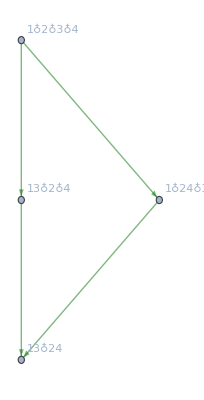
{-Graphics-360→{3,-Graphics-},-Graphics-354→{3,-Graphics-},-Graphics-352→{3,-Graphics-},-Graphics-336→{3,-Graphics-},-Graphics-334→{3,-Graphics-},-Graphics-328→{7/2,-Graphics-},-Graphics-282→{3,-Graphics-},-Graphics-280→{7/2,-Graphics-},-Graphics-274→{3,-Graphics-},-Graphics-256→{3,-Graphics-},-Graphics-120→{7/2,-Graphics-},-Graphics-118→{3,-Graphics-},-Graphics-112→{3,-Graphics-},-Graphics-94→{3,-Graphics-},-Graphics-40→{3,-Graphics-}}

```mathematica
Table[Labeled[allGraphs4[k,"graph"],Style[k,Red]]->{ChromaticPolynomial[allGraphs4[k,"graph"],4]/24,Graph[FormulaGraph[allGraphs4[k,"colofour"]],ImageSize->{Automatic,180},EdgeStyle->Directive[Opacity[0.5],Darker[Darker[Green]]]]},{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==4]&]}]
```

## Banded matrices

```mathematica
colorsBanded=Table[Table[If[OddQ[k],LightBlue,LightYellow],{i,StirlingS2[4,5-k]}],{k,1,4}]//Flatten
```

{RGBColor[0.87, 0.94, 1],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[1, 1, 0.85],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[0.87, 0.94, 1],RGBColor[1, 1, 0.85]}

```mathematica
colorsBanded2=Table[Table[If[OddQ[k],Red,Green],{i,StirlingS2[4,5-k]}],{k,1,4}]//Flatten
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]}

```mathematica
allGraphs4AtomKeysSorted=Sort[allGraphs4AtomKeys,CompareSymbols[allGraphs4[#1,"colofour"],allGraphs4[#2,"colofour"]]&];
```

```mathematica
allGraphs4NullAtomKeysSorted=Sort[allGraphs4NullAtomKeys,CompareSymbols[allGraphs4[#1,"colofourrealnull"],allGraphs4[#2,"colofourrealnull"]]&];
```

```mathematica
Vector4[key_]:=Table[Coefficient[allGraphs4[key,"colofourrealnull"],allGraphs4[k,"colofourrealnull"]],{k, allGraphs4NullAtomKeysSorted}]
```

```mathematica
Vector4Full[key_]:=Table[Coefficient[allGraphs4[key,"colofour"],allGraphs4[k,"colofour"]],{k, allGraphs4AtomKeysSorted}]
```

```mathematica
mob4=Table[
Mobius[allGraphs5[i,"vertexsets"],allGraphs5[j,"vertexsets"]]
,{i,allGraphs4NullAtomKeysSorted},{j,allGraphs4NullAtomKeysSorted}
]
```

{{Mobius[{{1},{2},{3},{4},{5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2},{3},{4},{5}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2},{3},{4,5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2},{3},{4,5}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2},{3,4},{5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2},{3,4},{5}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2},{3,5},{4}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2},{3,4,5}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,3},{4,5}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,3,4},{5}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,3,5},{4}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,4},{3,5}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,4,5},{3}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,5},{3,4}}],Mobius[{{1},{2},{3,5},{4}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,3},{4},{5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,3},{4},{5}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,4},{3},{5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,4},{3},{5}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,5},{3},{4}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,5},{3},{4}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2},{3,4,5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2},{3,4,5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2},{3,4,5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2},{3,4,5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2},{3,4,5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2},{3,4,5}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,3},{4,5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,3},{4,5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,3},{4,5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,3},{4,5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,3},{4,5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,3},{4,5}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,3,4},{5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,3,4},{5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,3,4},{5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,3,4},{5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,3,4},{5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,3,4},{5}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,3,5},{4}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,3,5},{4}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,3,5},{4}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,3,5},{4}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,3,5},{4}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,3,5},{4}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,4},{3,5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,4},{3,5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,4},{3,5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,4},{3,5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,4},{3,5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,4},{3,5}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,4,5},{3}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,4,5},{3}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,4,5},{3}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,4,5},{3}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,4,5},{3}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,4,5},{3}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,5},{3,4}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,5},{3,4}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,5},{3,4}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,5},{3,4}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,5},{3,4}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,5},{3,4}},{{1},{2,3,4,5}}]},{Mobius[{{1},{2,3,4,5}},{{1},{2},{3},{4},{5}}],Mobius[{{1},{2,3,4,5}},{{1},{2},{3},{4,5}}],Mobius[{{1},{2,3,4,5}},{{1},{2},{3,4},{5}}],Mobius[{{1},{2,3,4,5}},{{1},{2},{3,5},{4}}],Mobius[{{1},{2,3,4,5}},{{1},{2,3},{4},{5}}],Mobius[{{1},{2,3,4,5}},{{1},{2,4},{3},{5}}],Mobius[{{1},{2,3,4,5}},{{1},{2,5},{3},{4}}],Mobius[{{1},{2,3,4,5}},{{1},{2},{3,4,5}}],Mobius[{{1},{2,3,4,5}},{{1},{2,3},{4,5}}],Mobius[{{1},{2,3,4,5}},{{1},{2,3,4},{5}}],Mobius[{{1},{2,3,4,5}},{{1},{2,3,5},{4}}],Mobius[{{1},{2,3,4,5}},{{1},{2,4},{3,5}}],Mobius[{{1},{2,3,4,5}},{{1},{2,4,5},{3}}],Mobius[{{1},{2,3,4,5}},{{1},{2,5},{3,4}}],Mobius[{{1},{2,3,4,5}},{{1},{2,3,4,5}}]}}

```mathematica
TableForm[Table[Framed[If[mob4[[i,j]]==0,"",mob4[[i,j]]],Background->colorsBanded[[j]],ContentPadding->False,ImageSize->{30,30}, FrameStyle->Directive[colorsBanded2[[i]]]],{i,1,15},{j,1,15}],TableSpacing->{0, 0},TableHeadings->{Table[SymbolToLabel[allGraphs4[k,"colofour"]],{k,allGraphs4AtomKeysSorted}], Table[Rotate[SymbolToLabel[allGraphs4[k,"colofour"]],Pi/2],{k,allGraphs4AtomKeysSorted}]}]
```

1
 |  |  |  |

```mathematica
MatrixForm[{{1,-6,11,-6},{0,6,-18,12},{0,0,7,-7},{0,0,0,1}}]
```

(1 | -6 | 11 | -6
0 | 6 | -18 | 12
0 | 0 | 7 | -7
0 | 0 | 0 | 1)

```mathematica
MatrixForm[{{1,-6,11,-6},{0,6,-18,12}/6,{0,0,7,-7}/7,{0,0,0,1}}]
```

(1 | -6 | 11 | -6
0 | 1 | -3 | 2
0 | 0 | 1 | -1
0 | 0 | 0 | 1)

## Graphs and their complements

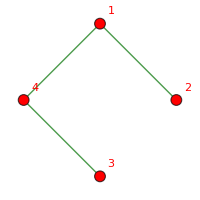
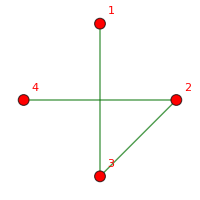
-Graphics-<->-Graphics-

```mathematica
Show[allGraphs4[271,"graph"],ImageSize->200]<->Show[allGraphs4[FindComplement[271,allGraphs4],"graph"],ImageSize->200]
```

```mathematica
SummaryPrintGood[271]
```

-Graphics-271-Graphics--n1234+n124x3+n12x34-n12x3x4+n134x2-n14x2x3-n1x2x34+n1x2x3x4x^4-3 x^3+3 x^2-x
(x-1)^3 x
 *  * 0224108320
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood[FindComplement[271,allGraphs4]]
```

-Graphics-93-Graphics--n1234+n123x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4x^4-3 x^3+3 x^2-x
(x-1)^3 x
 *  * 0224108320
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
allGraphs4[1,"colofour"]
```

v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4

```mathematica
Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,"colofour"]]]==4&&Length[Intersection[ListofVars[allGraphs4[#,"colofour"]],{v1x2x3x4,v12x3x4,v1x2x34,v12x34}]]==4&]
```

{120}

```mathematica
Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,"colofour"]]]==2&&Length[Intersection[ListofVars[allGraphs4[#,"colofour"]],{v1x2x3x4,v14x2x3}]]==2&]
```

{337}

```mathematica
allGraphs4[120,"graph"]
```

-Graphics-

```mathematica
allGraphs4[120,"colofourrealnull"]
```

-3 n1234+n123x4+n124x3+n134x2+n13x24-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4

```mathematica
allGraphs4[337,"graph"]
```

-Graphics-

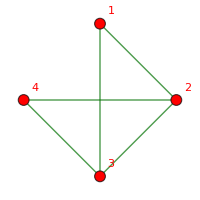
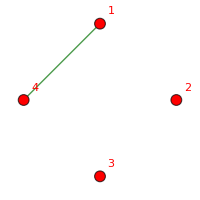
-Graphics-<->-Graphics-

```mathematica
Show[allGraphs4[337,"graph"],ImageSize->200]<->Show[allGraphs4[FindComplement[337,allGraphs4],"graph"],ImageSize->200]
```

```mathematica
SummaryPrintGood[337]
```

-Graphics-337-Graphics--4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+n134x2+n13x24-n13x2x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4x^4-5 x^3+8 x^2-4 x
(x-2)^2 (x-1) x
 *  * 00648180
-Graphics-+-Graphics-

```mathematica
SummaryPrintGood[FindComplement[337,allGraphs4]]
```

-Graphics-27-Graphics--n14x2x3+n1x2x3x4x^4-x^3
(x-1) x^3
 *  * 0854192500
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

## The annihilation game

```mathematica
Traverse[sets1_]:=Block[{sets,i,j, newset, result={}},
sets=Sort[Map[Sort[#]&,sets1]];
For[i=1,i≤Length[sets],i++,
For[j=i+1,j≤Length[sets],j++,
newset=sets;
newset=Delete[newset,j];
newset=Delete[newset,i];
newset=Append[newset,Sort[Flatten[Join[sets[[i]],sets[[j]]]]]];
newset=Sort[Map[Sort[#]&,newset]];
AppendTo[result, sets->newset];
result=Join[result,Traverse[newset]]
]
];
result
]
```

```mathematica
NormalizeSets[x_]:=Sort[Map[Sort[#]&,x],First[#1]<First[#2]&]
```

```mathematica
SetsToSymbol2[s_]:=Symbol["n"<>StringRiffle[Map[StringJoin[Map[ToString,#]]&,NormalizeSets[s]],"x"]]
```

```mathematica
Map[SetsToSymbol2[#[[1]]]->SetsToSymbol2[#[[2]]]&,Traverse[{{1,2},{3},{4}}]]
```

{n12x3x4→n12x34,n12x34→n1234,n12x3x4→n123x4,n123x4→n1234,n12x3x4→n124x3,n124x3→n1234}

```mathematica
Traverse[{{1,2},{3},{4}}]
```

{{{3},{4},{1,2}}→{{1,2},{3,4}},{{1,2},{3,4}}→{{1,2,3,4}},{{3},{4},{1,2}}→{{4},{1,2,3}},{{4},{1,2,3}}→{{1,2,3,4}},{{3},{4},{1,2}}→{{3},{1,2,4}},{{3},{1,2,4}}→{{1,2,3,4}}}

```mathematica
NormalizeSets[{{3},{4},{1,2}}]
```

{{1,2},{3},{4}}

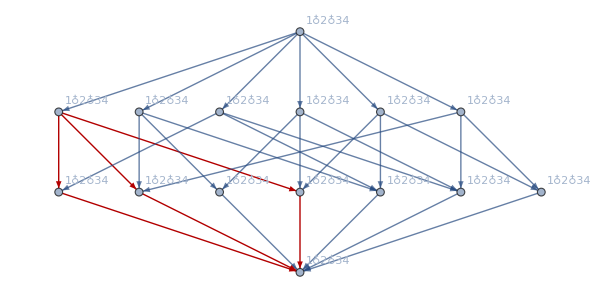

```mathematica
With[
{g=MobiusGraphSimple[K4Key,allGraphs4]},
Graph[
EdgeList[g],
VertexLabels->Table[SymbolToLabel[k],{k,VertexList[g]}],
GraphHighlight->Map[SetsToSymbol2[#[[1]]]->SetsToSymbol2[#[[2]]]&,Traverse[{{1,2},{3},{4}}]],
GraphHighlightStyle->"Thick",
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->600
]
]
```

```mathematica
With[
{g=MobiusGraphSimple[K4Key,allGraphs4]},
Graph[
EdgeList[g],
VertexLabels->Table[SymbolToLabel[k],{k,VertexList[g]}],
GraphHighlight->Map[SetsToSymbol2[#[[1]]]->SetsToSymbol2[#[[2]]]&,Traverse[{{1,2},{3},{4}}]],
GraphHighlightStyle->"Thick",
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->600
]
]
```

-Graphics-

## Intersection of lattices

```mathematica
h1=DeleteDuplicates[Traverse[{{1,5},{2},{3},{4}}]];
```

```mathematica
h2=DeleteDuplicates[Traverse[{{2,3},{1},{5},{4}}]];
```

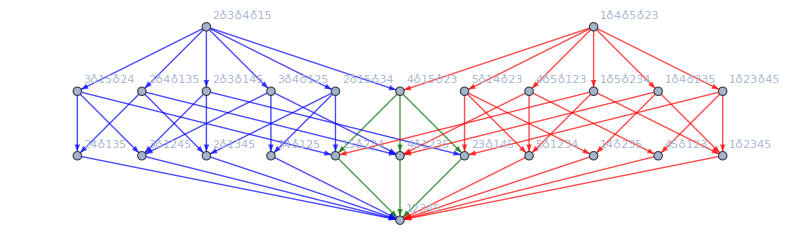

```mathematica
Graph[DeleteDuplicates[Join[h1,h2]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[h1,h2]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[h1,!MemberQ[h2,#]&]],
Map[#->Red&,Select[h2,!MemberQ[h1,#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[h1,h2]]
],
ImageSize->800]
```

```mathematica
g1=DeleteDuplicates[Traverse[{{1,5},{2},{3},{4}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{2,3},{1},{4},{5}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{4,2},{1},{3},{5}}]];
```

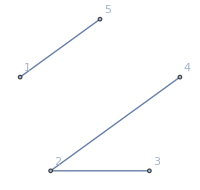

```mathematica
Graph[{1,2,3,4,5},{1<->5,2<->3,2<->4},GraphLayout->"CircularEmbedding", VertexLabels->"Name", ImageSize->200]
```

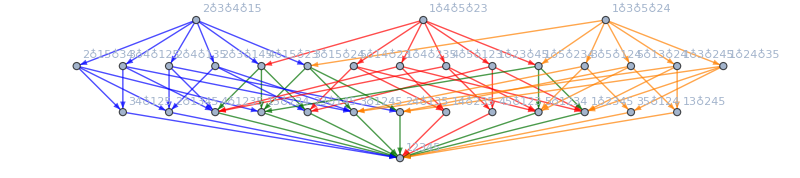

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[g1,!MemberQ[Union[g2,g3],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3],#]&]],
Map[#->Orange&,Select[g3,!MemberQ[Union[g2,g1],#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g3,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g3]]
],
ImageSize->800]
```

```mathematica
g1=DeleteDuplicates[Traverse[{{1,2},{3},{4},{5}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,3},{2},{4},{5}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{2,3},{1},{4},{5}}]];
```

```mathematica
Graph[{1,2,3,4,5},{1<->5,2<->3,2<->4},GraphLayout->"CircularEmbedding", VertexLabels->"Name", ImageSize->200]
```

-Graphics-

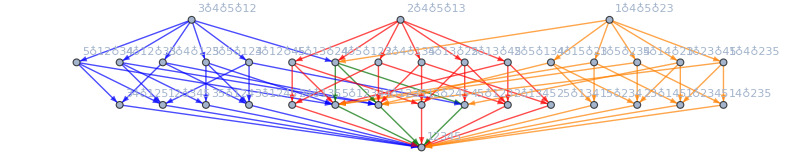

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[g1,!MemberQ[Union[g2,g3],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3],#]&]],
Map[#->Orange&,Select[g3,!MemberQ[Union[g2,g1],#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g3,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g3]]
],
ImageSize->800]
```